# UpSetChart Tests

```mathematica
Quit[];
```

```mathematica
$Path=Prepend[$Path,NotebookDirectory[]];
```

```mathematica
<<UpSetChart`Data`
```

```mathematica
sets=DummyData[1]
```

<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>

## The Packages of UpSetChart

## Unique Intersections

```mathematica
(* Calculates the unique elements for the comparisons *)
<<UpSetChart`UniqueIntersections`
```

```mathematica
UniqueIntersections[sets]
```

<|sets→<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>,setNames→{a,b,c,d,e},comparisons→{{},{a},{b},{c},{d},{e},{a,b},{a,c},{a,d},{a,e},{b,c},{b,d},{b,e},{c,d},{c,e},{d,e},{a,b,c},{a,b,d},{a,b,e},{a,c,d},{a,c,e},{a,d,e},{b,c,d},{b,c,e},{b,d,e},{c,d,e},{a,b,c,d},{a,b,c,e},{a,b,d,e},{a,c,d,e},{b,c,d,e},{a,b,c,d,e}},numberOfSets→5,elementsUniqueToComparisons→<|{}→{},{a,b,c,d,e}→{},{a,b,c,d}→{},{a,b,c,e}→{},{a,b,d,e}→{},{a,c,d,e}→{},{b,c,d,e}→{},{a,b,c}→{},{a,b,d}→{},{a,b,e}→{},{a,c,d}→{},{a,c,e}→{},{a,d,e}→{},{b,c,d}→{},{b,c,e}→{87},{b,d,e}→{},{c,d,e}→{},{a,b}→{},{a,c}→{},{a,d}→{},{a,e}→{},{b,c}→{},{b,d}→{90},{b,e}→{},{c,d}→{6},{c,e}→{15},{d,e}→{},{a}→{7,41,42,53,77,95},{b}→{37,51,67,88,96},{c}→{20,68,98,99},{d}→{46,85},{e}→{55,72,97}|>|>

## Utilities

```mathematica
(* Conditionals for types & passing down options *)
<<UpSetChart`Utilities`
```

## Calculations

```mathematica
(* Calls UniqueIntersections and sorts & filters data *)
<<UpSetChart`Calculations`
```

```mathematica
calc=CalcThenSortAndFilter[sets]
```

<|sets→<|a→{7,77,53,95,42,41},b→{51,88,87,67,90,37,96},c→{15,87,99,6,20,87,98,68},d→{46,85,6,90},e→{72,97,15,55,87}|>,comparisons→<|{a}→{7,41,42,53,77,95},{b}→{37,51,67,88,96},{c}→{20,68,98,99},{d}→{46,85},{e}→{55,72,97},{b,d}→{90},{c,d}→{6},{c,e}→{15},{b,c,e}→{87}|>|>

### Calculation Utilities

```mathematica
(* Sort & filter functions *)
<<UpSetChart`CalculationsUtilities`
```

## Graphics

```mathematica
(* Returns the graphics for UpSetChart *)
<<UpSetChart`Graphics`
```

### Utilities

```mathematica
(* Returns each components for the UpSetChart *)
<<UpSetChart`GraphicsUtilities`
```

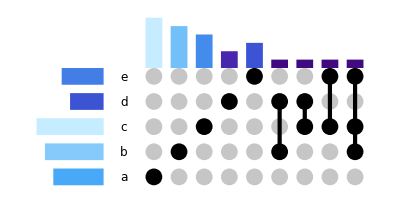

```mathematica
GraphicComponents[calc["sets"], calc["comparisons"]]//Graphics
```

#### Bar Chart

```mathematica
(* Components for charts *)
<<UpSetChart`GraphicsUtilitiesComparisonsBarChart`
```

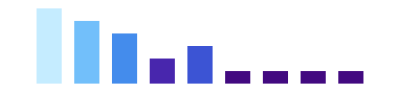

```mathematica
ComparisonsBarChart[calc["comparisons"],
 Max[Length/@calc["comparisons"]], Keys@calc["sets"]
]//Graphics[#,ImageSize->Tiny]&
```

#### Indicator

```mathematica
<<UpSetChart`GraphicsUtilitiesIndicatorGrid`
```

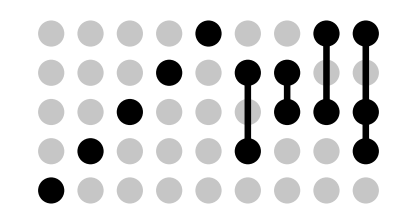

```mathematica
IndicatorGrid[Keys[calc["sets"]],Keys[calc["comparisons"]]]//Graphics[#,ImageSize->Tiny]&
```

#### Bar Chart

```mathematica
<<UpSetChart`GraphicsUtilitiesSetsBarChart`
```

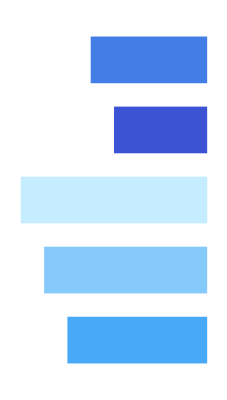

```mathematica
SetsBarChart[calc["sets"], Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

#### Labels

```mathematica
<<UpSetChart`GraphicsUtilitiesSetsLabels`
```

```mathematica
SetsLabels[ Keys[calc["sets"]], Max[Length/@calc["sets"]]]//Graphics[#,ImageSize->Tiny]&
```

-Graphics-